```mathematica
Clear[r];
phiG[r_] = 1/Sqrt[Pi]*Exp[-r]
phiE[r_] = (2-r)/(4*Sqrt[2*Pi])*Exp[-r/2]
phiEminus[r_, theta_, phi_] = r*Sin[theta]/(8*Sqrt[Pi])*Exp[-r/2-I*phi]
phiE0[r_, theta_] = r*Cos[theta]/(4*Sqrt[2*Pi])*Exp[-r/2]
phiEplus[r_, theta_, phi_] = -r*Sin[theta]/(8*Sqrt[Pi])*Exp[-r/2+I*phi]
phi1[r_, theta_, phi_, t_]=1/Sqrt[2Pi](phiG[r]+phiEminus[r,theta,phi]*Exp[-2I*Pi*t])
phi2[r_, theta_, phi_, t_]=1/Sqrt[2Pi](phiG[r]+phiE0[r,theta,phi]*Exp[-2I*Pi*t])
phi3[r_, theta_, phi_, t_]=1/Sqrt[2Pi](phiG[r]+phiEplus[r,theta,phi]*Exp[-2I*Pi*t])
phi11[r_, theta_, phi_, t_]=1/2*(phiG[r]*Conjugate[phiG[r]]+
phiG[r]*Conjugate[phiEminus[r,theta,phi]*Exp[-2I*Pi*t]]+
phiEminus[r,theta,phi]*Exp[-2I*Pi*t]*Conjugate[phiG[r]]+
phiEminus[r,theta,phi]*Exp[-2I*Pi*t]*Conjugate[phiEminus[r,theta,phi]*Exp[-2I*Pi*t]])
N[phi11[1,2,1,1]]
```

ⅇ^-r/(√π)

(ⅇ^(-r/2) (2-r))/(4 √(2 π))

(ⅇ^(-ⅈ phi-r/2) r Sin[theta])/(8 √π)

(ⅇ^(-r/2) r Cos[theta])/(4 √(2 π))

-(ⅇ^(ⅈ phi-r/2) r Sin[theta])/(8 √π)

(ⅇ^-r/(√π)+(ⅇ^(-ⅈ phi-r/2-2 ⅈ π t) r Sin[theta])/(8 √π))/(√(2 π))

(ⅇ^-r/(√π)+ⅇ^(-2 ⅈ π t) phiE0[r,theta,phi])/(√(2 π))

(ⅇ^-r/(√π)-(ⅇ^(ⅈ phi-r/2-2 ⅈ π t) r Sin[theta])/(8 √π))/(√(2 π))

1/2 (ⅇ^(-r-Conjugate[r])/π+(ⅇ^(-r+ⅈ Conjugate[phi]-Conjugate[r]/2+2 ⅈ π Conjugate[t]) Conjugate[r Sin[theta]])/(8 π)+(ⅇ^(-ⅈ phi-r/2-2 ⅈ π t-Conjugate[r]) r Sin[theta])/(8 π)+(ⅇ^(-ⅈ phi-r/2-2 ⅈ π t+ⅈ Conjugate[phi]-Conjugate[r]/2+2 ⅈ π Conjugate[t]) r Conjugate[r Sin[theta]] Sin[theta])/(64 π))

0.0266574+0. ⅈ

### Function 1

```mathematica
Xs = ConstantArray[0,5000];
Thetas = ConstantArray[0, 5000];
Phis = ConstantArray[0, 5000];
Coords = ConstantArray[0,5000];
Do [
Xs[[i]]= x/.FindRoot[RandomReal[]==1+ⅇ^(-2 x) (-1-2 x (1+x)), {x,0.001}];
Thetas[[i]]= ArcCos[1-2*RandomReal[]];
Phis[[i]]= 2Pi*RandomReal[];
Coords[[i]]={Xs[[i]],Thetas[[i]],Phis[[i]]};
,{i, 1, 5000}
]

chacha[{r_,theta_,phi_}] := {r*Sin[theta]*Cos[phi], r*Sin[theta]*Sin[phi], r*Cos[theta]}
```

```mathematica
ListPointPlot3D[Map[chacha, Coords],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
Integrate[4r^2*Exp[-2r],{r, 0, x}]
```

1+ⅇ^(-2 x) (-1-2 x (1+x))

### Function 2

```mathematica
Xs1 = ConstantArray[0,5000];
Thetas1 = ConstantArray[0, 5000];
Phis1 = ConstantArray[0, 5000];
Coords1 = ConstantArray[0,5000];
Do [
Xs1[[i]]= x/.FindRoot[RandomReal[]==1-1/8 ⅇ^-x (8+x (8+4 x+x^3)), {x,0.01}];
Thetas1[[i]]= ArcCos[1-2*RandomReal[]];
Phis1[[i]]= 2Pi*RandomReal[];
Coords1[[i]]={Xs1[[i]],Thetas1[[i]],Phis1[[i]]};
,{i, 1, 5000}
]
```

```mathematica
ListPointPlot3D[Map[chacha, Coords1],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

### Function 3

```mathematica
Xs2 = ConstantArray[0,15000];
Thetas2 = ConstantArray[0, 15000];
Phis2 = ConstantArray[0, 15000];
Coords2 = ConstantArray[0,15000];
Do [
Xs2[[i]]= x/.FindRoot[RandomReal[]==1+1/24 ⅇ^-x (-24-x (24+x (12+x (4+x)))), {x,0.01}];
Thetas2[[i]]= theta/.FindRoot[RandomReal[]== (2+Cos[theta]) Sin[theta/2]^4,{theta,0.01}];
Phis2[[i]]= 2Pi*RandomReal[];
Coords2[[i]]={Xs2[[i]],Thetas2[[i]],Phis2[[i]]};
,{i, 1, 15000}
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Integrate[(Exp[-r/2]*r)^2*r^2/24, {r, 0 ,x}]
Integrate[Sin[x]^3, {x, 0, theta}]
```

1+1/24 ⅇ^-x (-24-x (24+x (12+x (4+x))))

4/3 (2+Cos[theta]) Sin[theta/2]^4

```mathematica
ListPointPlot3D[Map[chacha, Coords2],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

### Function 4

```mathematica
Xs3 = ConstantArray[0,15000];
Thetas3 = ConstantArray[0, 15000];
Phis3 = ConstantArray[0, 15000];
Coords3 = ConstantArray[0,15000];
Do [
Xs3[[i]]= x/.FindRoot[RandomReal[]==1+1/24 ⅇ^-x (-24-x (24+x (12+x (4+x)))), {x,0.01}];
Thetas3[[i]]= theta/.FindRoot[RandomReal[]==1/3 (1-Cos[theta]^3),{theta,0.01}];
Phis3[[i]]= 2Pi*RandomReal[];
Coords3[[i]]={Xs3[[i]],Thetas3[[i]],Phis3[[i]]};
,{i, 1, 15000}
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
V[x_]=Integrate[Exp[-r]*r^2*4Pi*r^2/32/Pi/3, {r, 0 ,x}]
Limit[V[x], x-> Infinity]
Integrate[Sin[x]*Cos[x]^2, {x, -0, theta}]
```

1+1/24 ⅇ^-x (-24-x (24+x (12+x (4+x))))

1

1/3 (1-Cos[theta]^3)

```mathematica
ListPointPlot3D[Map[chacha, Coords3],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

ⅈ-ⅈ Cos[phi]+Sin[phi]

0

Integrate::ilim: Invalid integration variable or limit(s) in {0.0001,0,0.0001}.

NIntegrate::itraw: Raw object 0.0001 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.389057-0.969697 NIntegrate[1.9996,{0.0001,0,0.0001}]} is not a list of numbers with dimensions {1} at {x} = {0.0001}.

ReplaceAll::reps: {FindRoot[RandomReal[]==pr[x],{x,0.0001}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in {0.0001,0,0.0001}.

FindRoot::nlnum: The function value {0.928202-0.969697 NIntegrate[1.9996,{0.0001,0,0.0001}]} is not a list of numbers with dimensions {1} at {x} = {0.0001}.

ReplaceAll::reps: {FindRoot[RandomReal[]==pr[x],{x,0.0001}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in {0.0001,0,0.0001}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.10514-0.969697 NIntegrate[1.9996,{0.0001,0,0.0001}]} is not a list of numbers with dimensions {1} at {x} = {0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[RandomReal[]==pr[x],{x,0.0001}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{x/.FindRoot[RandomReal[]==pr[x],{x,0.0001}],-0.62898,5.68981}

```mathematica
N[Limit[pr[x],x->Infinity]]
```

NIntegrate::nlim: x = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate[1/64 ⅇ^(-2 Re[x]) (128+ⅇ^Re[x] x Conjugate[x]),{x,0,x}]

### Function 11

```mathematica
fr[r_, t_]=Integrate[phi11[r, theta, phi, t] r^2 Sin[theta], {theta, 0, Pi}, {phi, 0, 2Pi},Assumptions->{Im[r]==0,Im[t]==0}]
pr[r_,t_]=Integrate[fr[x,t],{x, 0, r}]


fphi[phi_, t_]=Integrate[phi11[r, theta, phi, t] r^2 Sin[theta], {r, 0, Infinity}, {theta, 0, Pi},Assumptions->{Im[r]==0,Im[t]==0,Im[phi]==0,Im[theta]==0}]
pphi[phi_,t_]=Integrate[fphi[x,t],{x, 0, phi}]


ftheta[theta_,t_]=Integrate[phi11[r, theta, phi, t] r^2 Sin[theta], {r, 0, Infinity}, {phi, 0, 2Pi},Assumptions->{Im[r]==0,Im[t]==0,Im[phi]==0,Im[theta]==0}]
ptheta[theta_,t_]=Integrate[ftheta[x,t],{x, 0, theta}]


Xs5 = ConstantArray[0,500];
Thetas5 = ConstantArray[0, 500];
Phis5 = ConstantArray[0, 500];
Coords5 = ConstantArray[0,500];
```

1/48 ⅇ^(-2 r) r^2 (96+ⅇ^r r^2)

1-1/2 ⅇ^(-2 r) (1+2 r+2 r^2)-1/48 ⅇ^-r (24+24 r+12 r^2+4 r^3+r^4)

1/(2 π)+2/27 Cos[phi+2 π t]

phi/(2 π)+2/27 (-Sin[2 π t]+Sin[phi+2 π t])

1/8 Sin[theta] (2+3 Sin[theta]^2)

1/32 (16-17 Cos[theta]+Cos[3 theta])

```mathematica
ListPointPlot3D[Map[chacha,Coords5],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
silly[t_]:=Do [
Xs5[[i]]= x/.FindRoot[RandomReal[]==pr[x,t], {x,0.001}];
Thetas5[[i]]= theta/.FindRoot[RandomReal[]==ptheta[theta,t],{theta,0.01}];
Phis5[[i]]= phi/.FindRoot[RandomReal[]==pphi[phi,t],{phi,0.01}];
Coords5[[i]]={Xs5[[i]],Thetas5[[i]],Phis5[[i]]};
,{i, 1, 500}
]
```

```mathematica
Print[Coords]
```

```mathematica
chacha[{r_,theta_,phi_}] := {r*Sin[theta]*Cos[phi], r*Sin[theta]*Sin[phi], r*Cos[theta]}
```

ListPointPlot3D::ldata: {0.176101+0.00391411 ⅈ,-0.291931+0.00749549 ⅈ,-0.21062-0.00711659 ⅈ} is not a valid dataset or list of datasets.

ListPointPlot3D[{0.176101+0.00391411 ⅈ,-0.291931+0.00749549 ⅈ,-0.21062-0.00711659 ⅈ}]

Integrate::ilim: Invalid integration variable or limit(s) in {0.+0.1 ⅈ,0,0.+0.1 ⅈ}.

NIntegrate::write: Tag Complex in 0.+0.1 ⅈ is Protected.

General::stop: Further output of NIntegrate::write will be suppressed during this calculation.

FindRoot::nlnum: The function value {-0.8+NIntegrate[1.93955+0. ⅈ,{0.+0.1 ⅈ,0,0.+0.1 ⅈ}]} is not a list of numbers with dimensions {1} at {x} = {0.+0.1 ⅈ}.

FindRoot[pr[x,1]==0.8,{x,0+0.1 ⅈ}]

```mathematica
Integrate[phi11[r, theta, phi, t] r^2 Sin[theta], {theta, 0, Pi}, {phi, 0, 2Pi},{r,0,Infinity},Assumptions->{Im[r]==0,Im[t]==0}]
```

1

```mathematica
fr[r_, t_]=Integrate[phi11[r, theta, phi, t] r^2 Sin[theta], {theta, 0, Pi}, {phi, 0, 2Pi},Assumptions->{Im[r]==0,Im[t]==0}]
pr[r_,t_]=Integrate[fr[x,t],{x, 0, r}]
```

1/48 ⅇ^(-2 r) r^2 (96+ⅇ^r r^2)

1-1/2 ⅇ^(-2 r) (1+2 r+2 r^2)-1/48 ⅇ^-r (24+24 r+12 r^2+4 r^3+r^4)

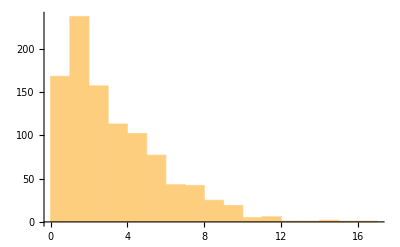

```mathematica
Table[x/.FindRoot[RandomReal[]==pr[x,0.1], {x,0.01}],{j,1,1000}]//Histogram
```

```mathematica
f1[r_, t_]=Integrate[phi11[r, theta, phi, t] r^2 Sin[theta], {phi, 0, 2Pi},Assumptions->{Im[r]==0,Im[t]==0, Im[theta]==0}]/(1/48 ⅇ^(-2 r) r^2 (96+ⅇ^r r^2))
```

(3 Sin[theta] (64+ⅇ^r r^2 Sin[theta]^2))/(4 (96+ⅇ^r r^2))

```mathematica
Integrate[f1[r,t],{theta, 0, Pi}]
```

1

```mathematica
Manipulate[
Plot[(3 Sin[theta] (64+ⅇ^r r^2 Sin[theta]^2))/(4 (96+ⅇ^r r^2)),{theta,0,Pi},PlotRange->All],{r,0,10}]
```